Get::noopen: Cannot open <pot_do_datoteke>/MonteCarloPi.m.

$Failed

MonteCarloPi[10000]

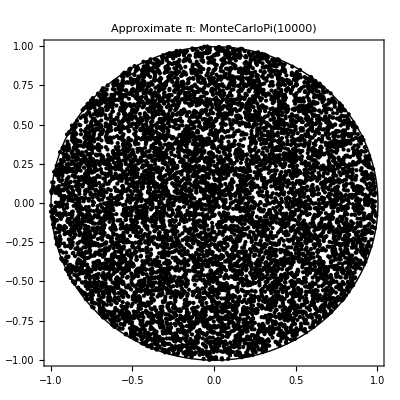

```mathematica
Get["<pot_do_datoteke>/MonteCarloPi.m"]

nPoints=10000;

approxPi=MonteCarloPi[nPoints]

randomPoints=RandomPoint[Disk[],nPoints];
Graphics[{Point[randomPoints],Circle[]},Frame->True,PlotLabel->Row[{"Approximate π: ",approxPi}]]
```